```mathematica
Clear[y,a,c,b,m,t0,po,pw,y0,v0,v,g,dt,po,pw,k1,k2,k3,M,dM,M0,t,IV,InV,Vol];

po=0.91745;
pi=0.9168;
pw=1;

g=980;
dt = 7.4;
m=25;
dM = 0.05*dt;
M[t_]:=12;
a=0.55;
R=0.5;
t0=5.9;

ve0=-1.8;
h0=26;

Vs[t_]:=(π/3) (3 R - (R/t0)t) (R t / t0)^2;
Vc[t_]:=(π R^2)(a ((t-t0)^2) + (R/t0)t - R);
Vol=(2/3)π R^3;
IV[t_] := Integrate[Vs[τ],{τ,0,t}] HeavisideTheta[t0-t] + (0.5890486225480862 + Integrate[Vc[τ] + Vol,{τ,t0,t}])HeavisideTheta[t-t0];
IV[τ]
```

(0.0037604 τ^3-0.000159339 τ^4) HeavisideTheta[5.9-τ]+(-29.3696+14.9059 τ-2.51534 τ^2+0.14399 τ^3) HeavisideTheta[-5.9+τ]

```mathematica
InV[t_]:=Integrate[(0.0037604048807691665 τ^3-0.0001593391898631003 τ^4) HeavisideTheta[5.9-τ]+(-29.36955853119647+14.905940843426274 τ-2.515337457029913 τ^2+0.1439896632895322 τ^3) HeavisideTheta[-5.9+τ],{τ,0,t}];
InV[t]
```

ConditionalExpression[HeavisideTheta[5.9-t] (t^4 (-29.5+1. t) (-0.0000318678 HeavisideTheta[-t]-0.0000318678 HeavisideTheta[t])-0.911324 HeavisideTheta[t])+(0.911324+(42.4223+t (-29.3696+t (7.45297+(-0.838446+0.0359974 t) t))) HeavisideTheta[-5.9+t]) HeavisideTheta[t],t∈ℝ]

```mathematica
InV[t_]:=ConditionalExpression[HeavisideTheta[5.9-t] (t^4 (-29.499999999999993+1. t) (-0.000031867837972620064 HeavisideTheta[-t]-0.000031867837972620064 HeavisideTheta[t])-0.9113236689288391 HeavisideTheta[t])+(0.9113236689288391+(42.422290557981036+t (-29.369558531196496+t (7.452970421713141+(-0.8384458190099715+0.03599741582238306 t) t))) HeavisideTheta[-5.9+t]) HeavisideTheta[t],t∈Reals];
```

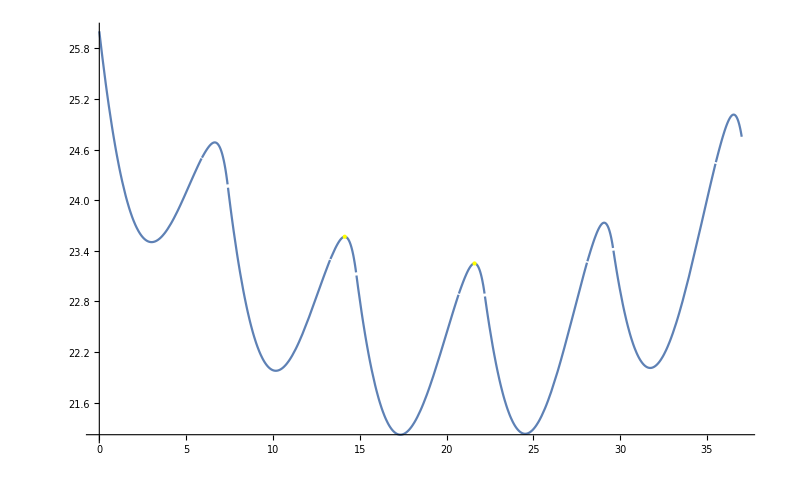

```mathematica
y[t_,v0_,y0_]:=((po*g/ m)*(1-(pw/pi)))*InV[t] + g*((po-pi)/(2*pi))*t^2 + y0 + v0*t;
v[t_,v0_]:=((po*g/ m)(1-(pw/pi)))*IV[t] + g*((po-pi)/(pi))t + v0;

y1=y[dt,ve0,h0];
v1=v[dt,ve0];
y2=y[dt,v1,y1];
v2=v[dt,v1];
y3=y[dt,v2,y2];
v3=v[dt,v2];
y4=y[dt,v3,y3];
v4=v[dt,v3];
y5=y[dt,v4,y4];
v5=v[dt,v4];
y6=y[dt,v5,y5];
v6=v[dt,v5];

Plot[Piecewise[{{y[t,ve0,h0], 0<=t<=dt}, {y[t-dt,v1,y1], dt<=t<=2 dt},{y[t-2 dt,v2,y2], 2 dt<=t<=3 dt},{y[t-3 dt,v3,y3], 3 dt<=t<=4 dt},{y[t-4 dt,v4,y4], 4dt<=t<=5 dt},{y[t-5dt,v5,y5], 5 dt<=t<6 dt}}],{t,0,5dt},Epilog->{{Yellow,PointSize@Large,Point[{21.61,y[6.81,v2,y2]}]},{Yellow,PointSize@Large,Point[{14.136,y[6.735999999999999,v1,y1]}]}}]
```

```mathematica
y[6.735999999999999,v1,y1]
```

23.5674

```mathematica
Man=Manipulate[ Graphics3D[{{Blue,Opacity[0.4],Cuboid[{-.5,-.5,-.5+ Piecewise[{{y[t,ve0,h0], 0<=t<dt}, {y[t-dt,v1,y1], dt<=t<2 dt},{y[t-2 dt,v2,y2], 2 dt<=t<3 dt},{y[t-3 dt,v3,y3], 3 dt<=t<4 dt},{y[t-4 dt,v4,y4], 4dt<=t<5 dt},{y[t-5dt,v5,y5], 5 dt<=t<6 dt}}]},{.5,.5,.5+ Piecewise[{{y[t,ve0,h0], 0<=t<dt}, {y[t-dt,v1,y1], dt<=t<2 dt},{y[t-2 dt,v2,y2], 2 dt<=t<3 dt},{y[t-3 dt,v3,y3], 3 dt<=t<4 dt},{y[t-4 dt,v4,y4], 4dt<=t<5 dt},{y[t-5dt,v5,y5], 5 dt<=t<6 dt}}]}]},{Yellow,Opacity[0.25],Cylinder[{{0,0,18},{0,0,26}},Scaled[0.15]]},{Opacity[0.1],Cylinder[{{0,0,18},{0,0,28}},Scaled[0.15]]}},PlotRange->{{-5,5},{-5,5},{15,30}},Boxed->False],
{t,0,4dt,0.001}]
```

```mathematica
Export["Sim1.avi",Man]
```

Sim1.avi

```mathematica
f[x_]:=Sin[x];
```

```mathematica
FindMaximum[f[x],{x,0}]
```

{1.,{x→1.5708}}

```mathematica
X=Range[0.01,dt,0.001];
Y1=y[X,v1,y1];
FindPeaks[Y1]
```

{{1,24.1506},{6727,23.5674}}

```mathematica
X[[6727]]
```

6.736

```mathematica
MAX=List[6.648,14.136,21.611,29.077,36.536,43.99,51.44]
```

{6.648,14.136,21.611,29.077,36.536,43.99,51.44}

```mathematica
MAXP=List[y[6.648,ve0,h0],y[14.136-dt,v1,y1],y[21.611-2dt,v2,y2],y[29.077-3dt,v3,y3],y[36.536-4dt,v4,y4],y[43.99-5dt,v5,y5],y[51.44-6dt,v6,y6]]
```

{24.6841,23.5674,23.2507,23.733,25.0132,27.0909,29.9655}

```mathematica
14.136-dt
```

6.736

```mathematica
Dif=List[MAX[[i+1]]-MAX[[i]],{i,1,4}]
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

{-{6.648,14.136,21.611,29.077,36.536,43.99,51.44}⟦i⟧+{6.648,14.136,21.611,29.077,36.536,43.99,51.44}⟦1+i⟧,{i,1,4}}

```mathematica
For[i=1,i<7,i++,Print[MAX[[i+1]]-MAX[[i]]]]
```

7.488

7.475

7.466

7.459

7.454

7.45

```mathematica
A=List[]
```

```mathematica
MAX[[8]]:=2;
MAX
```

SetDelayed::partw: Part 8 of {6.648,14.136,21.611,29.077,36.536,43.99,51.44} does not exist.

{6.648,14.136,21.611,29.077,36.536,43.99,51.44}